```mathematica
μ2=-2;
λ=1;
```

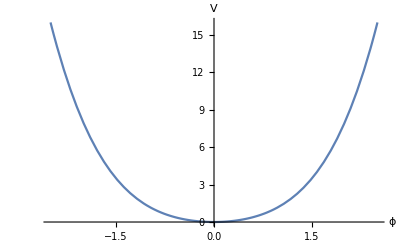

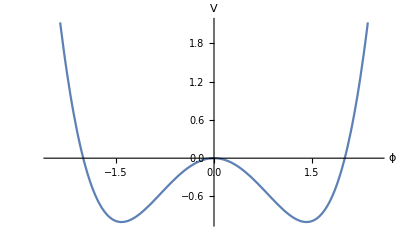

```mathematica
Plot[-1/2*μ2*ϕ^2+1/4*λ*ϕ^4,{ϕ,-2.5,2.5},AxesLabel->{HoldForm[ϕ],HoldForm[V]},LabelStyle->{13,GrayLevel[0]}]
Plot[1/2*μ2*ϕ^2+1/4*λ*ϕ^4,{ϕ,-2.5,2.5},AxesLabel->{HoldForm[ϕ],HoldForm[V]},LabelStyle->{13,GrayLevel[0]}]
```

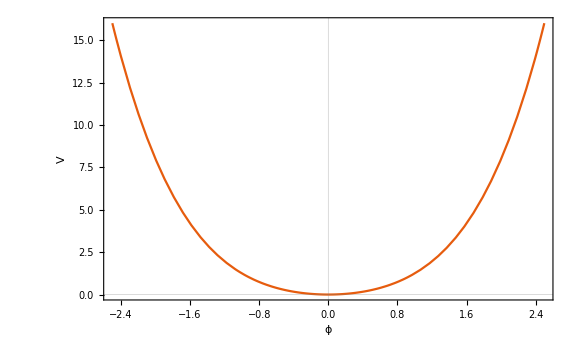

```mathematica
Plot[-(μ2 ϕ^2)/2+(λ ϕ^4)/4,{ϕ,-2.5,2.5},
PlotTheme->"Scientific",AxesLabel->{HoldForm[ϕ],HoldForm[V]},LabelStyle->{15,GrayLevel[0]},FrameLabel->{{HoldForm[V],None},{HoldForm[ϕ],None}},ImageSize->Large]
```

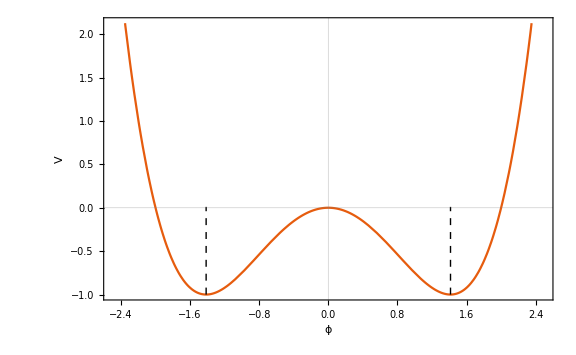

```mathematica
lineStyle={Thick,Black,Dashed};
line1=Line[{{√-μ2,-1},{√-μ2,0.01}}];
line2=Line[{{-√-μ2,-1},{-√-μ2,0.01}}];
Plot[(μ2 ϕ^2)/2+(λ ϕ^4)/4,{ϕ,-2.5,2.5},Epilog->{Directive[lineStyle],line1,line2},
PlotTheme->"Scientific",AxesLabel->{HoldForm[ϕ],HoldForm[V]},LabelStyle->{15,GrayLevel[0]},FrameLabel->{{HoldForm[V],None},{HoldForm[ϕ],None}},ImageSize->Large]
```

```mathematica
Plot3D[{1/2*μ2*(ϕ1^2+ϕ2^2)+1/4*λ*(ϕ1^2+ϕ2^2)^2},{ϕ1,-2,2},{ϕ2,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2<3.5],Exclusions->{ϕ1^2+ϕ2^2==-μ2/λ},ExclusionsStyle->({Directive[Opacity[1],Thick,Red]})]
```

-Graphics3D-

```mathematica
data={{√(-μ2/λ)+0.35,0,-0.8},{√(-μ2/λ),0.35,-0.8}};
Show[
Plot3D[{-1/50*μ2*(ϕ1^2+ϕ2^2)+1/15*λ*(ϕ1^2+ϕ2^2)^2},{ϕ1,-2,2},{ϕ2,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2<3.5], BoxRatios->Automatic,Boxed->False,Axes->False],
Graphics3D[{Red,Sphere[{0,0.,0.1},.1]}],
Graphics3D[{Black,Lighting->{{"Ambient",White}},Arrowheads[.02],Arrow[{{√(-μ2/λ),0,-0.8},#}]&/@data}],
Graphics3D[{Black,Lighting->{{"Ambient",White}},Arrowheads[.02],Arrow[{{-2,0,0},{2.2,0,0}}]&/@data}],
Graphics3D[{Black,Lighting->{{"Ambient",White}},Arrowheads[.02],Arrow[{{0,-2,0},{0,2.2,0}}]&/@data}]
]
```

-Graphics3D-

```mathematica
data={{√(-μ2/λ)+0.35,0,-0.8},{√(-μ2/λ),0.35,-0.8}};
Show[
Plot3D[{1/2*μ2*(ϕ1^2+ϕ2^2)+1/4*λ*(ϕ1^2+ϕ2^2)^2},{ϕ1,-2,2},{ϕ2,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2<3.5],Exclusions->{ϕ1^2+ϕ2^2==-μ2/λ},ExclusionsStyle->({Directive[Opacity[1],Thick,Black]}), BoxRatios->Automatic,Boxed->False,Axes->False],
Graphics3D[{Red,Sphere[{√(-μ2/λ),0.,-0.9},.1]}],
Graphics3D[{Black,Lighting->{{"Ambient",White}},Arrowheads[.02],Arrow[{{√(-μ2/λ),0,-0.8},#}]&/@data}],
Graphics3D[{Black,Lighting->{{"Ambient",White}},Arrowheads[.02],Arrow[{{-2,0,0},{2.2,0,0}}]&/@data}],
Graphics3D[{Black,Lighting->{{"Ambient",White}},Arrowheads[.02],Arrow[{{0,-2,0},{0,2.2,0}}]&/@data}]
]
```

-Graphics3D-